### Make smaller

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->200]&/@CellularAutomaton["GameOfLife",{$LifeData["Blinker"]["MatrixData"],0},24])[[i]], {i, 1, 24, 1}]
```

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{6,6}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->200]&/@CellularAutomaton["GameOfLife",{$LifeData["Blinker"]["MatrixData"],0},24])[[i]], {i, 1, 24, 1}]
```

```mathematica
CloudObject[["https://www.wolframcloud.com/obj/sw-writings/Video/Video-2025-03-05T18-42-32.mp4"](https://www.wolframcloud.com/obj/sw-writings/Video/Video-2025-03-05T18-42-32.mp4)]
```

Saved this to cloud, tried doing “GIF” it mangles the quality, so think it’s better to try to loop it from the html side.

Can also change the size that’s saved in the file if need be and/or slow the framerate down

### Put step numbers

I’ve always found it difficult to get a good sense of what’s going in a 2D cellular automaton by looking at a video.  With a class 4 rule like the Game of Life it often helps to have still frames that include “trails” of what’s happened before, and we’ll often use that type of visualization in what follows:

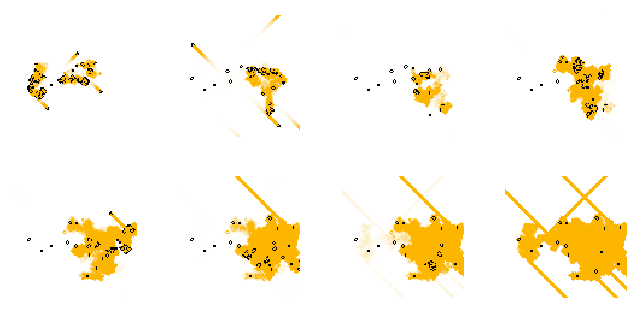

```mathematica
GraphicsGrid[Partition[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-50,50},{-50,50}},Mesh->(#<100),"Decay"-><|150->.9,300->.95,450-> .95, 600->.98,750->.985,900->.99,1050-> .995,  1200->.999|>[#]]&/@{150,300,450,600,750,900,1050,1200}, 4]]
```

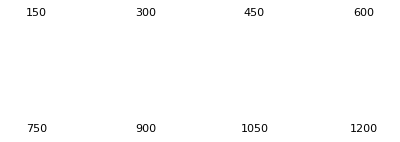

```mathematica
GraphicsGrid[Partition[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-50,50},{-50,50}},Mesh->(#<100),"Decay"-><|150->.9,300->.95,450-> .95, 600->.98,750->.985,900->.99,1050-> .995,  1200->.999|>[#]], Text[(*"step "<>*)ToString[#]]]&/@{150,300,450,600,750,900,1050,1200}, 4]]
```

### Generate 150, 300, 1200 steps. Label plots, etc.

To get a more global view of behavior it’s sometimes also useful to look at the whole (2+1)-dimensional “spacetime history”:

Generate 150, 300, 1200 steps.  In final case, cut off region so gliders poke through.
Label plots tucked on left underneath, in gray   (150 steps)   etc.

```mathematica
GraphicsRow[CellularAutomatonPlot3D["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#]&/@{150,300,1120}]
```

-Graphics-

Too big for me to run that 3rd one, getting the labels right here is a fricking nightmare and I think we need Brett

```mathematica
GraphicsRow[Table[GraphicsColumn[{CellularAutomatonPlot3D["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0}, 150(*, ImageSize->{10, 20}*)], Style[Text[150], Darker@Gray]},  Alignment->{Left, Center} , Spacings-> {Automatic, 20}(*Automatic*)(*, ImageSize->{20, 30}*), ImageSize->200], 3](*, ImageSize->650*)]
```

-Graphics-